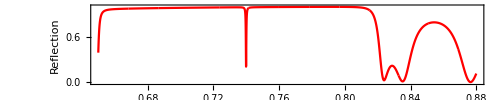

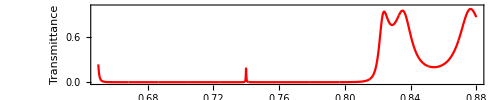

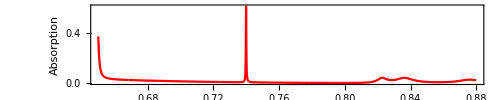

```mathematica
Clear["Global`*"];
d1=0.1;
d2=0.1;(*μm*)
Np=10;
Rsi=Import["TiO2.csv"][[1+Range[977]]];
Isi=Import["TiO2.csv"][[980+Range[977]]];
nRsi=Interpolation[Rsi,λ];nIsi=Interpolation[Isi,λ];n1=nRsi+nIsi*I;
rsio2=Import["SIO22.csv"][[1+Range[395]]];
isio2=Import["SIO22.csv"][[398+Range[395]]];
nrsio2=Interpolation[rsio2,λ];
nisio2=Interpolation[isio2,λ];
n2=nrsio2+nisio2*I;
Rh2o=Import["Kedenburg.csv"][[1+Range[101]]];
Ih2o =Import["Kedenburg.csv"][[104+Range[1011]]];
nRh2o=Interpolation[Rh2o,λ];nIh2o=Interpolation[Ih2o,λ];
nd=nRh2o+nIh2o*I;
Ret=Import["Aceton.csv"][[1+Range[101]]];
nRet=Interpolation[Ret,λ];net=nRet;

nddEMA=nd(2*Vet*(net-nd)+net+2nd)/(2*nd+net-Vet(net-nd));
θ=0;
b1=(1/λ)(2Pi*d1)n1*Cos[θ];
b2=(1/λ)(2Pi*d2)n2*Cos[θ];
bdd=((2Pi*dd)/λ)nddEMA*Cos[θ];
p1=n1 *Cos[θ]; 
p2 =n2 *Cos[θ];
pdd=nddEMA*Cos[θ];
L1={{Cos[b1],((-I)/p1)Sin[b1]},{-I*p1*Sin[b1],Cos[b1]}}; L2={{Cos[b2],((-I)/p2)Sin[b2]},{-I*p2*Sin[b2],Cos[b2]}};
Ldd={{Cos[bdd],((-I)/pdd)Sin[bdd]},{-I*pdd*Sin[bdd],Cos[bdd]}};
Q0 = 1;Qf =1;
dd=1;
стили оформления графиков;
labelT = {{"Transmittance",None},{"Wavelength,μm",None}};
labelR = {{"Reflection",None},{"Wavelength,μm",None}};
labelA = {{"Absorption",None},{"Wavelength,μm",None}};
label = {{"λ,μm",None},{"δ",None}};
style ={FontFamily->"Times New Roman",12,GrayLevel[0]};
color ={Red,Blue,Green,Yellow,Purple};
legend=SwatchLegend[color,{"0","0.25","0.5","0.75","1"} ,LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"Concentrations",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
RightWMS=MatrixPower[L2.L1,Np];
LeftWMS=MatrixPower[L2.L1,Np];
Mwms=RightWMS.Ldd.LeftWMS;M11WMS=Mwms[[1,1]];M12WMS=Mwms[[1,2]];M21WMS=Mwms[[2,1]];M22WMS=Mwms[[2,2]];
tWMS=(2*Q0)/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Twms =Abs[tWMS^2];
rWMS=((M11WMS+Qf*M12WMS)*Q0-(M21WMS+Qf*M22WMS))/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Rwms=Abs[rWMS^2];
rl=0.752;ll=0.765;
Awms=1-Rwms-Twms;
G1WMS = Plot[Rwms/.{dd->1,Vet->0.5},{λ,0.65,0.88},PlotRange->{-0.01,1},PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style,PlotPoints->100000,ClippingStyle->None]
G1WMS = Plot[Twms/.{dd->1,Vet->0.5},{λ,0.65,0.88},PlotRange->{-0.01,1},PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelT,LabelStyle->style,PlotPoints->100000,ClippingStyle->None]
G1WMS = Plot[Awms/.{dd->1,Vet->0.5},{λ,0.65,0.88},PlotRange->All,PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelA,LabelStyle->style,PlotPoints->100000,ClippingStyle->None]
```

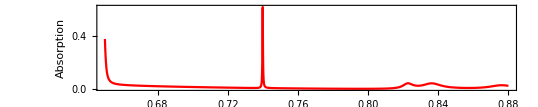

```mathematica
G1WMS = Plot[Awms/.{dd->1,Vet->0.5},{λ,0.65,0.88},PlotRange->All,PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelA,LabelStyle->style,PlotPoints->10000,ClippingStyle->None]
```